```mathematica
Quit
```

```mathematica
Get["C:\\Users\\COMPUTER\\ErasmoWorkspaces\\botfb\\FunctionalParsers.m"];
```

```mathematica
ebnfCode="
<parserProducts> = <adverb> , <verb> , [ <subject> ] , <object-spec> <@ ParserProducts[Flatten[#]]& ;
<verb> = ( 'cuesta' | 'queda' | 'es' ) <@ Verb ;
<object-spec> = ( <object-list> | <object> | <objects> | <objects-mult> ) <@ ProductsObjects[Flatten[{#}]]& ;
<adverb> = 'cuanto' | 'cual' | 'donde' <@ Adverb ;
<subject> = [ 'el' ] , 'precio' <@ Subj ;
<object> = [ 'kg' ] , 'de' , 'arroz' | 'leche' | 'azucar' | 'shampoo' ;
<objects> = 'fideos' | 'fresas' | [ 'kg' ] , 'de' , 'mandarinas' ;
<objects-mult> = 'Range[1,100]' , <objects> <@ Mult ;
<object-list> = ( <object> | <objects> | <objects-mult> ) , { 'y' ⊳ ( <object> | <objects> | <objects-mult> ) } ;";
```

```mathematica
ebnfCode="
<parserProducts> =  [ <adverb> ] , [ <verb> ] , [ <subject> ] , <object-spec> <@ ParserProducts[Flatten[#]]& ;
<verb> = ( 'cuesta' | 'queda' | 'es' | 'esta' ) <@ Verb ;
<object-spec> = ( <object-list> | <object> | <objects> | <objects-mult> ) <@ ProductsObjects[Flatten[{#}]]& ;
<presentation> = 'kilos' | 'kilo' | 'tarro' | 'kg' | 'botella' | 'botellas' | 'envase' | 'envases' | 'l' | 'litros' | 'paquete' | 'paquetes' <@ Presentation ;
<adverb> = [ 'a' ] , 'como' | 'cuanto' | 'cual' | 'donde' <@ Adverb ;
<subject> = [ 'el' ] ⊳ 'precio' ⊲ 'de' <@ Subj ;
<object> =  'arroz' | 'pollo' | 'chancho' | 'papel' , 'higienico' | 'aceite' | 'pan' | 'leche' | 'azucar' , [ 'rubia' ] | 'shampoo' | ( 'aceite' , 'de' , 'oliva' ) ;
<objects> = 'fideos' | 'tampones' | 'lavavajillas' | 'condones' | 'panes' | 'fresas' | 'mandarinas' ;
<objects-mult> = [ 'Range[1,100]' ] , [ <presentation> ] ,  [ 'de' ] ⊳ [ 'del' ] ⊳ [ 'la' ] ⊳ [ 'los' ] ⊳ [ 'las' ]  ⊳ ( <object> | <objects> ) <@ Mult ;
<object-list> = ( <object> | <objects> | <objects-mult> ) , { 'y' ⊳ ( <object> | <objects> | <objects-mult> ) } ;";
```

```mathematica
GenerateParsersFromEBNF[ToTokens[ebnfCode]]
```

{{{{},EBNF[{pPARSERPRODUCTS = ParseSequentialComposition[Block[{FunctionalParsers`Private`res=pADVERB[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialComposition[Block[{FunctionalParsers`Private`res=pVERB[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialComposition[Block[{FunctionalParsers`Private`res=pSUBJECT[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,pOBJECTSPEC]]]<@ParserProducts[Flatten[#]]&,pVERB = ParseAlternativeComposition[If[Length[#1]>0&&cuesta===First[#1],{{Rest[#1],cuesta}},{}]&,If[Length[#1]>0&&queda===First[#1],{{Rest[#1],queda}},{}]&,If[Length[#1]>0&&es===First[#1],{{Rest[#1],es}},{}]&,If[Length[#1]>0&&esta===First[#1],{{Rest[#1],esta}},{}]&]<@Verb,pOBJECTSPEC = ParseAlternativeComposition[pOBJECTLIST,pOBJECT,pOBJECTS,pOBJECTSMULT]<@ProductsObjects[Flatten[{#}]]&,pPRESENTATION = ParseAlternativeComposition[If[Length[#1]>0&&kilos===First[#1],{{Rest[#1],kilos}},{}]&,If[Length[#1]>0&&kilo===First[#1],{{Rest[#1],kilo}},{}]&,If[Length[#1]>0&&tarro===First[#1],{{Rest[#1],tarro}},{}]&,If[Length[#1]>0&&kg===First[#1],{{Rest[#1],kg}},{}]&,If[Length[#1]>0&&botella===First[#1],{{Rest[#1],botella}},{}]&,If[Length[#1]>0&&botellas===First[#1],{{Rest[#1],botellas}},{}]&,If[Length[#1]>0&&envase===First[#1],{{Rest[#1],envase}},{}]&,If[Length[#1]>0&&envases===First[#1],{{Rest[#1],envases}},{}]&,If[Length[#1]>0&&l===First[#1],{{Rest[#1],l}},{}]&,If[Length[#1]>0&&litros===First[#1],{{Rest[#1],litros}},{}]&,If[Length[#1]>0&&paquete===First[#1],{{Rest[#1],paquete}},{}]&,If[Length[#1]>0&&paquetes===First[#1],{{Rest[#1],paquetes}},{}]&]<@Presentation,pADVERB = ParseAlternativeComposition[ParseSequentialComposition[Block[{FunctionalParsers`Private`res=(If[Length[#1]>0&&a===First[#1],{{Rest[#1],a}},{}]&)[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,If[Length[#1]>0&&como===First[#1],{{Rest[#1],como}},{}]&],If[Length[#1]>0&&cuanto===First[#1],{{Rest[#1],cuanto}},{}]&,If[Length[#1]>0&&cual===First[#1],{{Rest[#1],cual}},{}]&,If[Length[#1]>0&&donde===First[#1],{{Rest[#1],donde}},{}]&]<@Adverb,pSUBJECT = ParseSequentialCompositionPickRight[Block[{FunctionalParsers`Private`res=(If[Length[#1]>0&&el===First[#1],{{Rest[#1],el}},{}]&)[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialCompositionPickLeft[If[Length[#1]>0&&precio===First[#1],{{Rest[#1],precio}},{}]&,If[Length[#1]>0&&de===First[#1],{{Rest[#1],de}},{}]&]]<@Subj,pOBJECT = ParseAlternativeComposition[If[Length[#1]>0&&arroz===First[#1],{{Rest[#1],arroz}},{}]&,If[Length[#1]>0&&pollo===First[#1],{{Rest[#1],pollo}},{}]&,If[Length[#1]>0&&chancho===First[#1],{{Rest[#1],chancho}},{}]&,ParseSequentialComposition[If[Length[#1]>0&&papel===First[#1],{{Rest[#1],papel}},{}]&,If[Length[#1]>0&&higienico===First[#1],{{Rest[#1],higienico}},{}]&],If[Length[#1]>0&&aceite===First[#1],{{Rest[#1],aceite}},{}]&,If[Length[#1]>0&&pan===First[#1],{{Rest[#1],pan}},{}]&,If[Length[#1]>0&&leche===First[#1],{{Rest[#1],leche}},{}]&,ParseSequentialComposition[If[Length[#1]>0&&azucar===First[#1],{{Rest[#1],azucar}},{}]&,Block[{FunctionalParsers`Private`res=(If[Length[#1]>0&&rubia===First[#1],{{Rest[#1],rubia}},{}]&)[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&],If[Length[#1]>0&&shampoo===First[#1],{{Rest[#1],shampoo}},{}]&,ParseSequentialComposition[If[Length[#1]>0&&aceite===First[#1],{{Rest[#1],aceite}},{}]&,ParseSequentialComposition[If[Length[#1]>0&&de===First[#1],{{Rest[#1],de}},{}]&,If[Length[#1]>0&&oliva===First[#1],{{Rest[#1],oliva}},{}]&]]],pOBJECTS = ParseAlternativeComposition[If[Length[#1]>0&&fideos===First[#1],{{Rest[#1],fideos}},{}]&,If[Length[#1]>0&&tampones===First[#1],{{Rest[#1],tampones}},{}]&,If[Length[#1]>0&&lavavajillas===First[#1],{{Rest[#1],lavavajillas}},{}]&,If[Length[#1]>0&&condones===First[#1],{{Rest[#1],condones}},{}]&,If[Length[#1]>0&&panes===First[#1],{{Rest[#1],panes}},{}]&,If[Length[#1]>0&&fresas===First[#1],{{Rest[#1],fresas}},{}]&,If[Length[#1]>0&&mandarinas===First[#1],{{Rest[#1],mandarinas}},{}]&],pOBJECTSMULT = ParseSequentialComposition[Block[{FunctionalParsers`Private`res=ParseApply[ToExpression,ParsePredicate[StringMatchQ[#1,NumberString]&&1≤ToExpression[#1]≤100&]][#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialComposition[Block[{FunctionalParsers`Private`res=pPRESENTATION[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialCompositionPickRight[Block[{FunctionalParsers`Private`res=(If[Length[#1]>0&&de===First[#1],{{Rest[#1],de}},{}]&)[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialCompositionPickRight[Block[{FunctionalParsers`Private`res=(If[Length[#1]>0&&del===First[#1],{{Rest[#1],del}},{}]&)[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialCompositionPickRight[Block[{FunctionalParsers`Private`res=(If[Length[#1]>0&&la===First[#1],{{Rest[#1],la}},{}]&)[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialCompositionPickRight[Block[{FunctionalParsers`Private`res=(If[Length[#1]>0&&los===First[#1],{{Rest[#1],los}},{}]&)[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseSequentialCompositionPickRight[Block[{FunctionalParsers`Private`res=(If[Length[#1]>0&&las===First[#1],{{Rest[#1],las}},{}]&)[#1]},If[TrueQ[FunctionalParsers`Private`res==={}],{{#1,{}}},FunctionalParsers`Private`res]]&,ParseAlternativeComposition[pOBJECT,pOBJECTS]]]]]]]]<@Mult,pOBJECTLIST = ParseSequentialComposition[ParseAlternativeComposition[pOBJECT,pOBJECTS,pOBJECTSMULT],ParseMany1[ParseSequentialCompositionPickRight[If[Length[#1]>0&&y===First[#1],{{Rest[#1],y}},{}]&,ParseAlternativeComposition[pOBJECT,pOBJECTS,pOBJECTSMULT]]]]}]}},{}}

```mathematica
sentences= {"del arroz","cuanto cuesta 1 tarro de leche","cual es el precio de 1 kg de mandarinas","cual es el precio de 2 botellas de aceite de oliva","cuanto cuesta 1 l de leche y 5 kg de azucar rubia", "cuanto cuesta 3 kg de azucar rubia","a como esta kilo de fideos","3 envases de shampoo","cuanto esta 1 l de leche","5 kg de arroz","lavavajillas","8 kilos de pollo"}
```

{del arroz,cuanto cuesta 1 tarro de leche,cual es el precio de 1 kg de mandarinas,cual es el precio de 2 botellas de aceite de oliva,cuanto cuesta 1 l de leche y 5 kg de azucar rubia,cuanto cuesta 3 kg de azucar rubia,a como esta kilo de fideos,3 envases de shampoo,cuanto esta 1 l de leche,5 kg de arroz,lavavajillas,8 kilos de pollo}

```mathematica
ParsingTestTable[pPARSERPRODUCTS,ToLowerCase@sentences,"Layout"->"Vertical"]
```

1 | command: | del arroz
 | parsed: | ParserProducts[{ProductsObjects[{Mult[{{},{{},arroz}}]}]}]
 | residual: | {}
2 | command: | cuanto cuesta 1 tarro de leche
 | parsed: | ParserProducts[{Adverb[cuanto],Verb[cuesta],ProductsObjects[{Mult[{1,{Presentation[tarro],leche}}]}]}]
 | residual: | {}
3 | command: | cual es el precio de 1 kg de mandarinas
 | parsed: | ParserProducts[{Adverb[cual],Verb[es],Subj[precio],ProductsObjects[{Mult[{1,{Presentation[kg],mandarinas}}]}]}]
 | residual: | {}
4 | command: | cual es el precio de 2 botellas de aceite de oliva
 | parsed: | ParserProducts[{Adverb[cual],Verb[es],Subj[precio],ProductsObjects[{Mult[{2,{Presentation[botellas],aceite}}]}]}]
 | residual: | {de,oliva}
5 | command: | cuanto cuesta 1 l de leche y 5 kg de azucar rubia
 | parsed: | ParserProducts[{Adverb[cuanto],Verb[cuesta],ProductsObjects[{Mult[{1,{Presentation[l],leche}}],Mult[{5,{Presentation[kg],{azucar,rubia}}}]}]}]
 | residual: | {}
6 | command: | cuanto cuesta 3 kg de azucar rubia
 | parsed: | ParserProducts[{Adverb[cuanto],Verb[cuesta],ProductsObjects[{Mult[{3,{Presentation[kg],{azucar,rubia}}}]}]}]
 | residual: | {}
7 | command: | a como esta kilo de fideos
 | parsed: | ParserProducts[{Adverb[{a,como}],Verb[esta],ProductsObjects[{Mult[{{},{Presentation[kilo],fideos}}]}]}]
 | residual: | {}
8 | command: | 3 envases de shampoo
 | parsed: | ParserProducts[{ProductsObjects[{Mult[{3,{Presentation[envases],shampoo}}]}]}]
 | residual: | {}
9 | command: | cuanto esta 1 l de leche
 | parsed: | ParserProducts[{Adverb[cuanto],Verb[esta],ProductsObjects[{Mult[{1,{Presentation[l],leche}}]}]}]
 | residual: | {}
10 | command: | 5 kg de arroz
 | parsed: | ParserProducts[{ProductsObjects[{Mult[{5,{Presentation[kg],arroz}}]}]}]
 | residual: | {}
11 | command: | lavavajillas
 | parsed: | ParserProducts[{ProductsObjects[{lavavajillas}]}]
 | residual: | {}
12 | command: | 8 kilos de pollo
 | parsed: | ParserProducts[{ProductsObjects[{Mult[{8,{Presentation[kilos],pollo}}]}]}]
 | residual: | {}

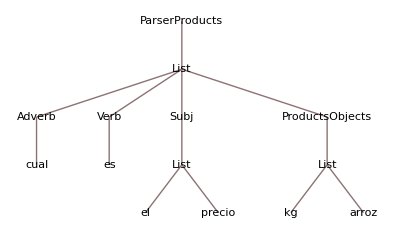

```mathematica
TreeForm[ParserProducts[{Adverb["cual"],Verb["es"],Subj[{"el","precio"}],ProductsObjects[{"kg","arroz"}]}]]
```

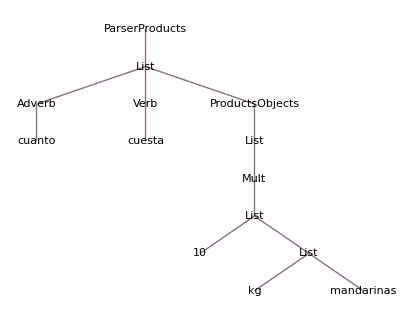

```mathematica
TreeForm[ParserProducts[{Adverb["cuanto"],Verb["cuesta"],ProductsObjects[{Mult[{10,{"kg","mandarinas"}}]}]}]]
```

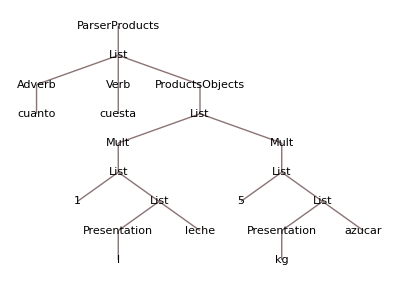

```mathematica
TreeForm[ParserProducts[{Adverb["cuanto"],Verb["cuesta"],ProductsObjects[{Mult[{1,{Presentation["l"],"leche"}}],Mult[{5,{Presentation["kg"],"azucar"}}]}]}]]
```

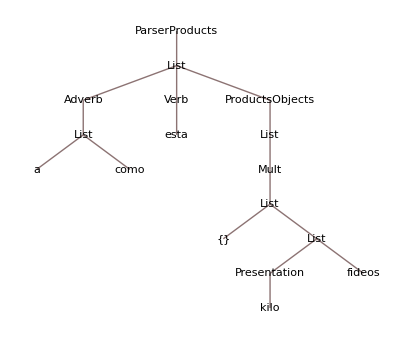

```mathematica
TreeForm[ParserProducts[{Adverb[{"a","como"}],Verb["esta"],ProductsObjects[{Mult[{{},{Presentation["kilo"],"fideos"}}]}]}]]
```